### Соотношения

```mathematica
Subscript[ε, xx]=D[Subscript[u, 1][x,y], x];
Subscript[ε, yy]=D[Subscript[u, 2][x,y], y];
Subscript[ε, xy]=1/2(D[Subscript[u, 1][x,y], y]+D[Subscript[u, 2][x,y], x]);
Subscript[σ, xx]=(λ+2μ)(Subscript[ε, xx]-Subscript[α, xx] T[x,y,t])+λ(Subscript[ε, yy]-Subscript[α, yy] T[x,y,t]);
Subscript[σ, yy]=(λ+2μ)(Subscript[ε, yy]-Subscript[α, yy] T[x,y,t])+λ(Subscript[ε, xx]-Subscript[α, xx] T[x,y,t]);
Subscript[σ, xy]=2μ(Subscript[ε, xy]-Subscript[α, xy] T[x,y,t]);
Subscript[σ, yx]=2μ(Subscript[ε, yx]-Subscript[α, yx] T[x,y,t]);
```

### Уравнение равновесия

```mathematica
eq1=v[x,y](D[Subscript[σ, xx], x]+D[Subscript[σ, yx], y]+Subscript[f, x][x,y])
```

v[x,y] (f_x[x,y]-2 μ α_yx T^(0,1,0)[x,y,t]+(λ+2 μ) (u_1^(2,0)[x,y]-α_xx T^(1,0,0)[x,y,t])+λ (u_2^(1,1)[x,y]-α_yy T^(1,0,0)[x,y,t]))

### Переписал с ТеХа

```mathematica
(∫_0)^d(v[x,y]((λ+2μ)(D[Subscript[u, 1][x,y], x]-Subscript[α, xx] T[x,y,t])+λ(D[Subscript[u, 2][x,y], y]-Subscript[α, yy] T[x,y,t]))(|_0)^b-(∫_0)^b D[v[x,y], x]((λ+2μ)(D[Subscript[u, 1][x,y], x]-Subscript[α, xx] T)+λ(D[Subscript[u, 2][x,y], y]-Subscript[α, yy] T[x,y,t]))ⅆx)ⅆy+(∫_0)^b(μv[x,y]((D[Subscript[u, 1][x,y], y]+D[Subscript[u, 2][x,y], x])-Subscript[α, yx] T[x,y,t])(|_0)^d-(∫_0)^d μ D[v[x,y], y]((D[Subscript[u, 1][x,y], y]+D[Subscript[u, 2][x,y], x])-Subscript[α, yx] T[x,y,t])ⅆy)ⅆx+(∫_0)^b(∫_0)^d v[x,y] Subscript[f, x] ⅆyⅆx
```

### Слева все известно, справа нет

```mathematica
(∫_0)^d(v[x,y]((λ+2μ)(D[Subscript[u, 1][x,y], x]-Subscript[α, xx] T[x,y,t])+λ(D[Subscript[u, 2][x,y], y]-Subscript[α, yy] T[x,y,t])))(|_0)^b ⅆy+(∫_0)^b(μv[x,y]((D[Subscript[u, 1][x,y], y]+D[Subscript[u, 2][x,y], x])-Subscript[α, yx] T[x,y,t]))(|_0)^d ⅆx +(∫_0)^b(∫_0)^d v[x,y] Subscript[f, x] ⅆyⅆx=(∫_0)^d(∫_0)^b D[v[x,y], x]((λ+2μ)(D[Subscript[u, 1][x,y], x]-Subscript[α, xx] T)+λ(D[Subscript[u, 2][x,y], y]-Subscript[α, yy] T[x,y,t]))ⅆxⅆy+(∫_0)^b(∫_0)^d μ D[v[x,y], y]((D[Subscript[u, 1][x,y], y]+D[Subscript[u, 2][x,y], x])-Subscript[α, yx] T[x,y,t])ⅆyⅆx
```

```mathematica
Subscript[fun, 1]=(v[x,y]((λ+2μ)(D[Subscript[u, 1][x,y], x]-Subscript[α, xx] T[x,y,t])+λ(D[Subscript[u, 2][x,y], y]-Subscript[α, yy] T[x,y,t]))/.podstan)
```

ReplaceAll::reps: {podstan} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

v[x,y] (λ (-α_yy T[x,y,t]+u_2^(0,1)[x,y])+(λ+2 μ) (-α_xx T[x,y,t]+u_1^(1,0)[x,y]))/.podstan

### Подстановка

```mathematica
podstan= {Subscript[u, 1][x, y] -> ∑_(i=1)^N Subscript[ϕ, i][x,y] Subscript[u, 1,i], Subscript[u, 2][x,y] -> ∑_(i=1)^N Subscript[ϕ, i][x,y] Subscript[u, 2,i]};
Subscript[u, 1][x,y]:=∑_(i=1)^N Subscript[ϕ, i][x,y] Subscript[u, 1,i];
Subscript[u, 2][x,y]:=∑_(i=1)^N Subscript[ϕ, i][x,y] Subscript[u, 2,i];
```

```mathematica
(∫_0)^d(v[x,y]((λ+2μ)(D[Subscript[u, 1][x,y], x]-Subscript[α, xx] T[x,y,t])+λ(D[Subscript[u, 2][x,y], y]-Subscript[α, yy] T[x,y,t])))(|_0)^b ⅆy+(∫_0)^b(μv[x,y]((D[Subscript[u, 1][x,y], y]+D[Subscript[u, 2][x,y], x])-Subscript[α, yx] T[x,y,t]))(|_0)^d ⅆx +(∫_0)^b(∫_0)^d v[x,y] Subscript[f, x] ⅆyⅆx=(∫_0)^d(∫_0)^b D[v[x,y], x]((λ+2μ)(D[Subscript[u, 1][x,y], x]-Subscript[α, xx] T)+λ(D[Subscript[u, 2][x,y], y]-Subscript[α, yy] T[x,y,t]))ⅆxⅆy+(∫_0)^b(∫_0)^d μ D[v[x,y], y]((D[Subscript[u, 1][x,y], y]+D[Subscript[u, 2][x,y], x])-Subscript[α, yx] T[x,y,t])ⅆyⅆx
```

## Метод конечных элементов

### Область

```mathematica
reg=Rectangle[{0,0},{1,1}];
```

### Максимальная площадь треугольника

```mathematica
Smax = 0.5;
```

### Создание сетки

```mathematica
Needs["NDSolve`FEM`"]
mesh =ToElementMesh[reg,MaxCellMeasure->Smax,"MeshOrder"->1,"MeshElementType"->"TriangleElement","NodeReordering"->True];
```

```mathematica
mesh1 = MeshRegion[mesh];
```

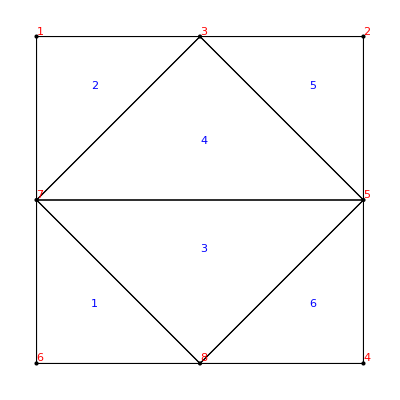

```mathematica
Show[mesh["Wireframe"["MeshElement"->"MeshElements","MeshElementIDStyle"->Blue,"ContinuousElementID"->True]],mesh["Wireframe"["MeshElement"->"PointElements","MeshElementIDStyle"->Red]]]
```

#### Координаты узлов

```mathematica
nodescoordinates=MeshCoordinates[mesh1]
```

{{0.,1.},{1.,1.},{0.5,1.},{1.,0.},{1.,0.5},{0.,0.},{0.,0.5},{0.5,0.}}

#### Количество узлов и элементов

```mathematica
nodNum=MeshCellCount[mesh1,0]
elNum=MeshCellCount[mesh1,2]
```

8

6

#### Номера узлов для каждого элемента

```mathematica
elementnodesnumbers=MeshCells[mesh1,2][[;;,1]]
elementnodesnumbers[[1]]
```

{{6,8,7},{3,1,7},{7,8,5},{5,3,7},{2,3,5},{5,8,4}}

{6,8,7}

#### Координаты узлов для каждого элемента

```mathematica
elementnodescoordinates=nodescoordinates[[#]]&/@elementnodesnumbers
```

{{{0.,0.},{0.5,0.},{0.,0.5}},{{0.5,1.},{0.,1.},{0.,0.5}},{{0.,0.5},{0.5,0.},{1.,0.5}},{{1.,0.5},{0.5,1.},{0.,0.5}},{{1.,1.},{0.5,1.},{1.,0.5}},{{1.,0.5},{0.5,0.},{1.,0.}}}

#### Граничные ребра (с номерами узлов) и номера всех узлов на границе

```mathematica
boundaryedges=mesh["BoundaryElements"][[1,1]]
boundarynodes=DeleteDuplicates@Flatten@boundaryedges
```

{{8,6},{6,7},{1,3},{7,1},{4,8},{5,4},{2,5},{3,2}}

{8,6,7,1,3,4,5,2}

#### Функции формы на произвольном элементе

```mathematica
Subscript[NN, 1][ξ_,η_]:=1-ξ-η
Subscript[NN, 2][ξ_,η_]:=ξ
Subscript[NN, 3][ξ_,η_]:=η
Fx[{{x1_,y1_},{x2_,y2_},{x3_,y3_}},ξ_,η_]:=(x2-x1)ξ + (x3-x1)η + x1
Fy[{{x1_,y1_},{x2_,y2_},{x3_,y3_}},ξ_,η_]:= (y2-y1)ξ + (y3-y1)η + y1
```

#### Локальная матрица жесткости и правая часть

```mathematica
a=(-y1+y3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
b=(x1-x3)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
d=(y1-y2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
e=(-x1+x2)/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3));
```

```mathematica
J={{a,b},{d,e}};
```

```mathematica
Transpose[J].Grad[Subscript[NN, i][ξ,η],{ξ,η}].Transpose[J].Grad[Subscript[NN, j][ξ,η],{ξ,η}]
```

NN_j^(0,1)[ξ,η] (((-x1+x2) (((-x1+x2) NN_i^(0,1)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))+((x1-x3) NN_i^(1,0)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))+((y1-y2) (((y1-y2) NN_i^(0,1)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))+((-y1+y3) NN_i^(1,0)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3)))+(((x1-x3) (((-x1+x2) NN_i^(0,1)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))+((x1-x3) NN_i^(1,0)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))+((-y1+y3) (((y1-y2) NN_i^(0,1)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))+((-y1+y3) NN_i^(1,0)[ξ,η])/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))))/(x3 (y1-y2)+x1 (y2-y3)+x2 (-y1+y3))) NN_j^(1,0)[ξ,η]

```mathematica
ktemp[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=Evaluate@Table[Integrate[Transpose[J].Grad[Subscript[NN, i][ξ,η],{ξ,η}].Transpose[J].Grad[Subscript[NN, j][ξ,η],{ξ,η}],{ξ,η}∈Triangle[{{0,0},{1,0},{0,1}}]],{i,3},{j,3}];
```

```mathematica
Kloc[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=Evaluate[2*Area[Triangle[{{x1,y1},{x2,y2},{x3,y3}}]]*ktemp[{{x1,y1},{x2,y2},{x3,y3}}]]
Floc[{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=2*Area[Triangle[{{x1,y1},{x2,y2},{x3,y3}}]]*Table[FullSimplify@NIntegrate[-Subscript[NN, i][ξ,η]f[Fx[{{x1,y1},{x2,y2},{x3,y3}},ξ,η],Fy[{{x1,y1},{x2,y2},{x3,y3}},ξ,η]],{ξ,η}∈Triangle[{{0,0},{1,0},{0,1}}]],{i,3}]
```

#### Сборка глобальной матрицы жесткости и правой части

```mathematica
Kglobal=ConstantArray[0,{nodNum,nodNum}];
For[i=1,i<=elNum,i++,Kglobal[[elementnodesnumbers[[i]],elementnodesnumbers[[i]]]]+=Kloc[elementnodescoordinates[[i]]]]
Fglobal=ConstantArray[0,{nodNum}]; 
For[i=1,i<=elNum,i++,Fglobal[[elementnodesnumbers[[i]]]]+=Floc[elementnodescoordinates[[i]]]]
```

NIntegrate::inumr: The integrand (-1+η+ξ) f[0.+0.5 ξ,0.+0.5 η] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand -ξ f[0.+0.5 ξ,0.+0.5 η] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

#### Задание граничного условия Дирихле

NIntegrate::inumr: The integrand (-1+η+ξ) f[0.5-0.5 η-0.5 ξ,1.-0.5 η-1.42109×10^-14 ξ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand (-1+η+ξ) f[1.-0.5 ξ,1.-0.5 η] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

NIntegrate::inumr: The integrand (-1+η+ξ) f[0.5-0.5 η-0.5 ξ,1.-0.5 η-1.42109×10^-14 ξ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1},{0,1}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

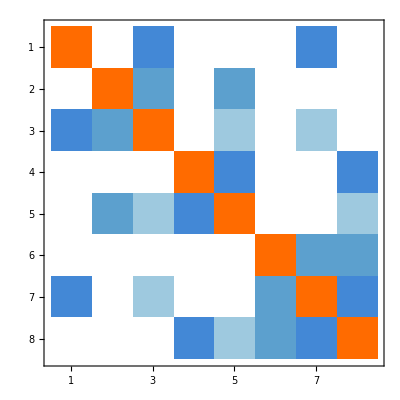

```mathematica
For[i=1,i<=Length@boundarynodes,++i,Kglobal[[boundarynodes[[i]],boundarynodes[[i]]]]+=10^20;Fglobal[[boundarynodes[[i]]]]+=10^20 u0]
MatrixPlot[Kglobal]
```

### Решение и построения графика

```mathematica
usol=Quiet@LinearSolve[Kglobal,Fglobal];
plotsol=Table[Flatten[{nodescoordinates[[i]],usol[[i]]}],{i,nodNum}];
Show[pl,ListPlot3D[plotsol,PlotStyle->Opacity[0.5]]]
```

$Aborted

Part::partd: Part specification usol⟦1⟧ is longer than depth of object.

Part::partd: Part specification usol⟦2⟧ is longer than depth of object.

Part::partd: Part specification usol⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[pl,].

Show[pl,-Graphics3D-]